## SpaRTaNS Tutorial: Double Chamber Flow

## Last updated: 04/30/2022

## Material Properties

Source Code

```mathematica
projectionOperator[vector_]:=IdentityMatrix[Length[vector]]-KroneckerProduct[vector,vector]

meanLifetime[sMC_]:=Mean[1/divideByZeroGivesZero[Diagonal[sMC]]]
divideByZeroGivesZero=Chop[#]/. 0|0. ->∞&;
numberOfStates=48;
```

```mathematica
Clear[isotropicScatteringMatricesSymmetric2D]
isotropicScatteringMatricesSymmetric2D[n_]:=Block[{angles,velocityProjection,normalizedEnergy,energyProjection,kpts,vels,sm,smVelocityRelaxed,smVelocityProjected},

kpts=N[AngleVector/@Most[Subdivide[π/n,2π+π/n,n]]];
vels=N[AngleVector/@Most[Subdivide[π/n,2π+π/n,n]]];

velocityProjection=Dot@@projectionOperator/@Orthogonalize[Prepend[Transpose[vels],ConstantArray[1,n]],Method->"GramSchmidt"];
normalizedEnergy=ConstantArray[1/√n,n];
energyProjection=projectionOperator[normalizedEnergy];

sm=Normal[SparseArray[{i_,i_}:>n-1.,{n,n},-1.]/n];

smVelocityRelaxed=energyProjection.DiagonalMatrix[Diagonal[sm]].energyProjection;
smVelocityProjected=velocityProjection.sm.velocityProjection;

{kpts,vels,sm,smVelocityProjected,smVelocityRelaxed}

]

scaledIsotropicScatteringMatrix2D[m_][{τMC_,∞}]:=Block[{kpts,vels,numeric,sMC,sMR,β,α},
{kpts,vels,numeric,sMC,sMR}=isotropicScatteringMatricesSymmetric2D[m];
α=1/τMC meanLifetime[sMC];
{kpts,vels,numeric,sMC,sMR,α sMC}
]
```

Material Properties

We will consider a 2D isotropic material (SO2)

Using a 48 states discretization

We will consider a material in the “Hydrodynamic” Regime

l_MC/W ~ 0.2, l_MR/W → ∞

The group velocities and scattering matrix are plotted below

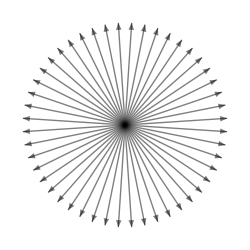
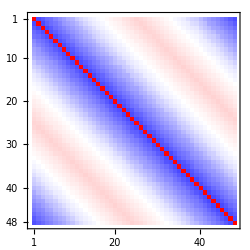
-Graphics- | -Graphics-

```mathematica
{kpts["SO2"],vels["SO2"],numeric["SO2"],smMomentumConserving["SO2"],smMomentumRelaxing["SO2"],sm["SO2"]}=scaledIsotropicScatteringMatrix2D[numberOfStates][{100,∞}];

With[{cf=(Blend[{Blue,White,Red},#]&)},
Multicolumn[{Graphics[{{Opacity[0.5],Arrow[{{0,0},#}]&/@vels["SO2"]}},ImageSize->250],
MatrixPlot[sm["SO2"],PlotLegends->LinearGradientImage[{Bottom,Top}->cf,{30,300}],ImageSize->250,ColorFunction->cf]
},2]]
```

We split the scattering matrix into diagonal and mixing-matrix components

```mathematica
diagonal["SO2"]=Diagonal[sm["SO2"]];
mixingMatrix["SO2"]=sm["SO2"]-DiagonalMatrix[diagonal["SO2"]];
```

Since all states are on the Fermi surface, we set the energies to the same value of 1

```mathematica
frequencies["SO2"]=ConstantArray[1.,numberOfStates];
```

Finally, we pad the 2D velocities with zeros for the out-of-plane direction

```mathematica
velocities["SO2"]=ArrayPad[vels["SO2"],{{0,0},{0,1}}]//N;
```